## Calibrating the Clayton copula

```mathematica
data = Import["~/Documents/GitHub/optimal_hedging_ratio_copula/processed_data/coingecko_future_v1/train/0.csv"];
```

```mathematica
returns=data⟦2;;All,5;;6⟧;
```

Clayton with empirical marginals; From the documentation:

```mathematica
{{, {"Clayton",c}, (∑_i^n Subscript[u, i]^(-1/c)-1)^-c, Clayton–Pareto copula}}
```

(       | {Clayton,c} | (∑_i^n u_i^(-1/c)-1)^-c | Clayton–Pareto copula)

Note that θ=1/c

```mathematica
clayton=CopulaDistribution[{"Clayton",1/θ},{SmoothKernelDistribution[returns⟦1;;All,1⟧],SmoothKernelDistribution[returns⟦1;;All,2⟧]}];
```

Clayton copula

```mathematica
claytoncopula=CopulaDistribution[{"Clayton",1/θ},{UniformDistribution[],UniformDistribution[]}];
```

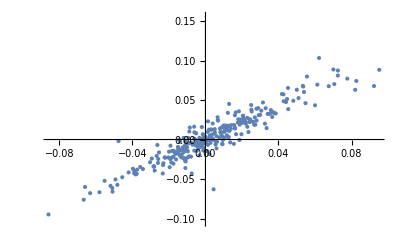

```mathematica
ListPlot[returns]
```

```mathematica
NMaximize[{∑_(k=1)^Length[returns] Log[PDF[clayton,returns⟦k⟧]],θ>0},{θ,1,10}]
```

{1505.05,{θ→5.68848}}

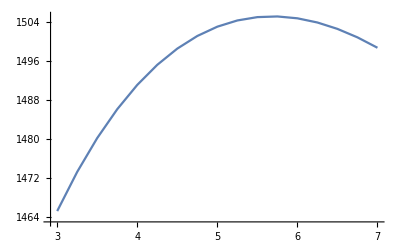

```mathematica
ListPlot[Table[{θ,∑_(k=1)^Length[returns] Log[PDF[clayton,returns⟦k⟧]]},{θ,3,7,0.25}],Joined->True]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
target = Join[{SpearmanRho[returns][[1,2]]}, Table[QDemp[q,returns⟦;;,1⟧,returns⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}]]
```

{0.932246,0.933333,0.866667,0.9,0.8}

```mathematica
obj={θ/(θ+2), CDF[claytoncopula, {0.05, 0.05}]/0.05, CDF[claytoncopula, {0.1, 0.1}]/0.1, (1-2 0.9 + CDF[claytoncopula, {0.9, 0.9}])/(1-0.9), (1-2 0.95 + CDF[claytoncopula, {0.95, 0.95}])/(1-0.95)}
```

{θ/(θ+2),20. (2 0.05^-θ-1)^(-1/θ),10. (2 0.1^-θ-1)^(-1/θ),10. ((2 0.9^-θ-1)^(-1/θ)-0.8),20. ((2 0.95^-θ-1)^(-1/θ)-0.9)}

```mathematica
NMinimize[{Total[(obj-target)^2],θ>0},θ]
```

{0.0192693,{θ→59.0216}}

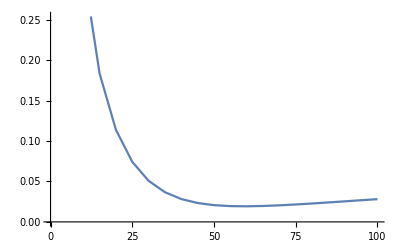

```mathematica
ListPlot[Table[{θ,Total[(obj-target)^2]},{θ,5,100,5}],Joined->True]
```

Spearman’s Rho

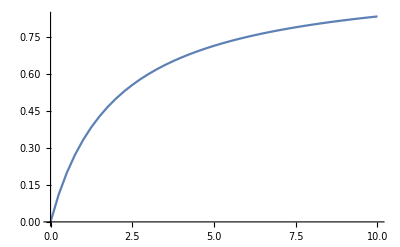

```mathematica
ListPlot[Table[{θ, θ/(θ+2)}, {θ, 0,10,0.25}],Joined->True]
```

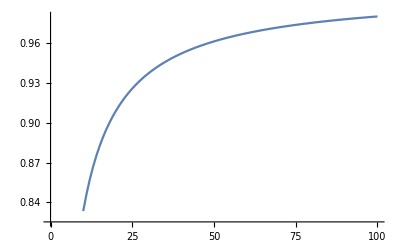

```mathematica
ListPlot[Table[{θ, θ/(θ+2)}, {θ,10,100}],Joined->True]
```

Spearman’s Rho for the two results

```mathematica
N[{θ/(θ+2)/.θ->5.68, θ/(θ+2)/.θ->59}]
```

{0.739583,0.967213}

```mathematica
p
```